```mathematica
sc1=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\AB.csv"];
scMerge=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\merge.csv"];
scTop=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\AB_Top.csv"];
```

```mathematica
Grid[sc1,Frame->All];
Grid[scMerge,Frame->All];
Grid[scTop,Frame->All];
```

```mathematica
Union[sc1[[;;,2]]];
Union[scMerge[[;;,4]]];
Union[scTop[[;;,2]]]
```

{ABBIE,BOBBY,JERRY,JUDGE HOFFMAN,KUNSTLER,RENNIE,SCHULTZ,Speaker,TOM,WEINGLASS}

```mathematica
SortBy[Tally[sc1[[;;,2]]],Last];
```

```mathematica
SortBy[Tally[scMerge[[;;,4]]],Last];
```

```mathematica
SortBy[Tally[scTop[[;;,2]]],Last]
```

{{Speaker,1},{WEINGLASS,41},{RENNIE,51},{BOBBY,59},{JERRY,91},{SCHULTZ,99},{ABBIE,113},{JUDGE HOFFMAN,134},{TOM,154},{KUNSTLER,189}}

```mathematica
ch = sc1[[;;,2]];
chMerge= scMerge[[;;,4]];
chTop= scTop[[;;,2]];
```

```mathematica
e1=Table[ch[[i]]<->ch[[i+1]],{i,1,Length[ch]-1}];
e2=Table[ch[[i]]->ch[[i+1]],{i,1,Length[ch]-1}];

e1Mrg=Table[chMerge[[i]]<->chMerge[[i+1]],{i,1,Length[chMerge]-1}];
e2Mrg=Table[chMerge[[i]]->chMerge[[i+1]],{i,1,Length[chMerge]-1}];

e1Top=Table[chTop[[i]]<->chTop[[i+1]],{i,1,Length[chTop]-1}];
e2Top=Table[chTop[[i]]->chTop[[i+1]],{i,1,Length[chTop]-1}];
```

```mathematica
v1 = Union[ch];
v1Mrg = Union[chMerge]; 
v1Top= Union[chTop];
```

```mathematica
<->
```

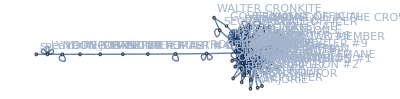

```mathematica
UndirectedWeightedGraph1=Graph[v1,e1,VertexLabels->"Name"] ;
UndirectedNonWeightedGraph2=SimpleGraph[UndirectedWeightedGraph1];
DirectedWeightedGraph3=Graph[v1,e2,VertexLabels->"Name"];
DirectedNonWeightedGraph4=SimpleGraph[DirectedWeightedGraph3];

MergeUndirectedWeightedGraph1=Graph[v1Mrg,e1Mrg,VertexLabels->"Name"]
```

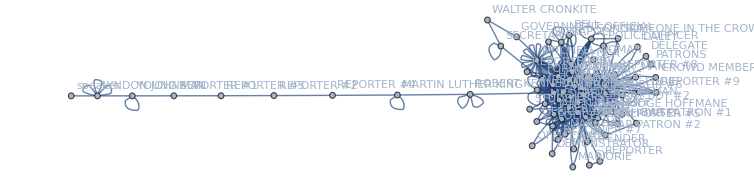

```mathematica
s1
```

```mathematica
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph1.jpg", UndirectedWeightedGraph1]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph2.jpg", UndirectedNonWeightedGraph2]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph3.jpg", DirectedWeightedGraph3]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph4.jpg", DirectedNonWeightedGraph4]
```

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph1.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph2.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph3.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph4.jpg

```mathematica
DegreeCentrality[UndirectedWeightedGraph1];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],DegreeCentrality[UndirectedWeightedGraph1]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedNonWeightedGraph2],DegreeCentrality[UndirectedNonWeightedGraph2]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedWeightedGraph3],DegreeCentrality[DirectedWeightedGraph3]}],Last]
```

{{LYNDON JOHNSON,1},{BARTENDER,2},{CROWD MEMBER,2},{DALEY,2},{DELEGATE,2},{DEMONSTRATOR,2},{FRAT BOY #1,2},{FRAT BOY #2,2},{GOVERNMENT OFFICIAL,2},{JACK,2},{MAN,2},{MARJORIE,2},{MARSHAL,2},{MARTIN LUTHER KING,2},{MRS. DELLINGER,2},{MRS. WINTER,2},{OFFICER,2},{OFFICER #2,2},{OFFICER QUINN,2},{PATRONS,2},{POLICE OFFICER,2},{PROTESTORS,2},{REPORTER,2},{REPORTER #1,2},{REPORTER #2,2},{REPORTER #3,2},{REPORTER #4,2},{REPORTER #5,2},{REPORTER #6,2},{REPORTER #7,2},{REPORTER #8,2},{REPORTER #9,2},{ROBERT KENNEDY,2},{SOMEONE IN THE CROWD,2},{SONDRA,2},{STUDENT,2},{SY,2},{WALTER CRONKITE,2},{WOMAN,2},{ALL,3},{CROWD,3},{SON,3},{BAR PATRON #1,4},{BELL,4},{EDDIE,4},{FRAPOLY,4},{JANE,4},{JUROR #6,4},{SECRETARY,4},{YOUNG MAN,4},{FRAT BOYS,5},{MITCHELL,5},{SAM,5},{BAR PATRON #2,6},{FRED,6},{POLICEMAN,6},{BAILIFF,7},{WOJOHOWSKI,7},{SCOTT,8},{WEINER,8},{DELUCA,9},{FROINES,10},{BERNADINE,11},{HOWARD,11},{FORAN,12},{CLARK,13},{STAHL,13},{BOBBY,15},{DAPHNE,15},{CUT BACK TO:,20},{RENNIE,21},{DAVE,23},{WEINGLASS,25},{JUDGE HOFFMAN,31},{TOM,36},{SCHULTZ,37},{JERRY,40},{ABBIE,49},{KUNSTLER,54}}

```mathematica
SortBy[Transpose[{VertexList[DirectedNonWeightedGraph4],DegreeCentrality[DirectedNonWeightedGraph4]}],Last];
```

```mathematica
PageRankCentrality[UndirectedWeightedGraph1,0.85];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],PageRankCentrality[UndirectedWeightedGraph1,0.85]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedNonWeightedGraph2],PageRankCentrality[UndirectedNonWeightedGraph2,0.85]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedWeightedGraph3],PageRankCentrality[DirectedWeightedGraph3,0.85]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedNonWeightedGraph4],PageRankCentrality[DirectedNonWeightedGraph4,0.85]}],Last];

ClosenessCentrality[UndirectedWeightedGraph1];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],ClosenessCentrality[UndirectedWeightedGraph1]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedNonWeightedGraph2],ClosenessCentrality[UndirectedNonWeightedGraph2]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedWeightedGraph3],ClosenessCentrality[DirectedWeightedGraph3]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedNonWeightedGraph4],ClosenessCentrality[DirectedNonWeightedGraph4]}],Last];
```

## 2) compute the 4 graph on the merge.csv file (AB-srt.csv)

```mathematica
MrgUndirectedWeightedGraph1=Graph[v1Mrg,e1Mrg,VertexLabels->"Name",ImageSize->Full] ;
MrgUndirectedNonWeightedGraph2=SimpleGraph[MrgUndirectedWeightedGraph1, ImageSize->Full];
MrgDirectedWeightedGraph3=Graph[v1Mrg,e2Mrg,VertexLabels->"Name", ImageSize->Full];
MrgDirectedNonWeightedGraph4=SimpleGraph[MrgDirectedWeightedGraph3, ImageSize->Full];
```

Export pictures

```mathematica
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph1.jpg", UndirectedWeightedGraph1]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph2.jpg", UndirectedNonWeightedGraph2]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph3.jpg", DirectedWeightedGraph3]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph4.jpg", DirectedNonWeightedGraph4]
```

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph1.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph2.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph3.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph4.jpg

## New AB graph of 8 peopl:

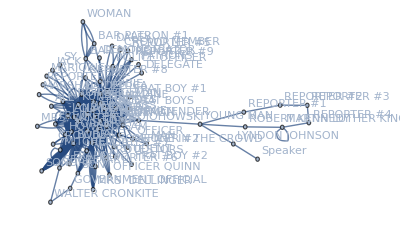

```mathematica
UndirectedWeightedGraph1
```

```mathematica
names=Take[SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],VertexDegree[UndirectedWeightedGraph1]}],Last],{-8,-1}][[;;,1]]
```

{RENNIE,BOBBY,JERRY,SCHULTZ,ABBIE,JUDGE HOFFMAN,TOM,KUNSTLER}

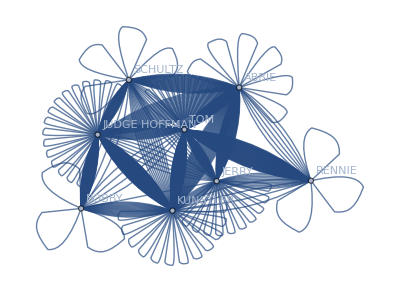

```mathematica
TopgGraph=Subgraph[UndirectedWeightedGraph1,names,VertexLabels->"Name"]
```

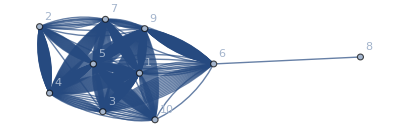

VertexDelete::inv: The argument {\"\<BARTENDER\>\", \"\<CROWD MEMBER\>\", \"\<DALEY\>\", \"\<DELEGATE\>\", \"\<DEMONSTRATOR\>\", \"\<FRAT BOY #\>\", \"\<FRAT BOY #2\>\", \"\<GOVERNMENT OFFICIAL\>\", \"\<JACK\>\", \"\<LYNDON JOHNSON\>\", «60»} in PaneBox[\"\\\"\<VertexDelete[Graph[<79>, <1285>], {BARTENDER, CROWD MEMBER, DALEY, DELEGATE, DEMONSTRATOR, FRAT BOY #, FRAT BOY #2, GOVERNMENT OFFICIAL, JACK, LYNDON JOHNSON, <<60>>}]\>\\\"\",BaselinePosition->Baseline] is not a valid \"\<vertex\>\".

```mathematica
adj=AdjacencyMatrix[TopUndirectedWeightedGraph1];
Do[adj[[i,i]]=0,{i,1,Length[adj]}];
AdjacencyGraph[adj,VertexLabels->Automatic]
```